Code developed for, and used in, the following publication, please cite appropriately:

Opening up baryon-number-violating operators
Julian Heeck, Diana Sokhashvili, Anil Thapa
arXiv:2603.17050
https://arxiv.org/abs/2603.17050

Related code and more information can also be found at
https://julian-heeck.github.io/BNV/

# Generate tree-level Feynman-diagram topologies

```mathematica
(* Set the working directory as notebook Directory *)
SetDirectory[NotebookDirectory[]]
```

## Generate topologically inequivalent tree graphs

First, we generate the topologies. Our procedure  is  to  define  a  function  “addVertices”  that  takes  a  list  of  graphs  and  generates  new  graphs  by  adding  vertices  and  edges  to  existing  vertices  in  each  graph. In essence, it adds one internal particle line or propagator.
The key part is If[VertexDegree[g, v] == 1, ...], which  checks  if  a vertex has  degree  1, i.e. is an external particle.  If  true,  it  proceeds  to  create  new  graph  by  adding  edges  connected  to  this  vertex. We only add cubic and quartic vertices since we are interested in renormalizable interactions.

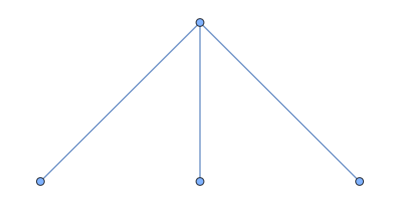
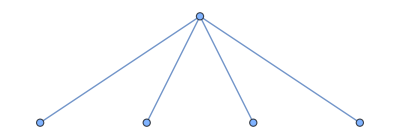
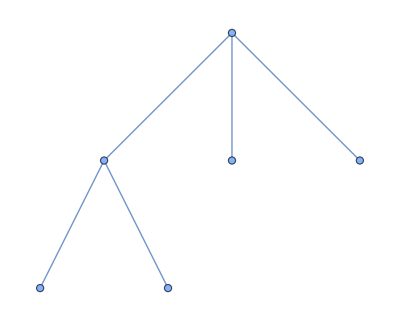
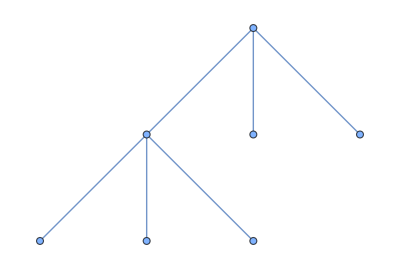
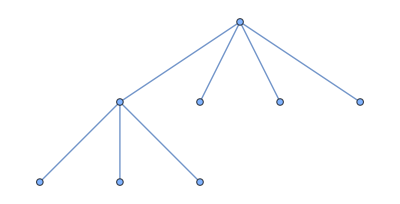
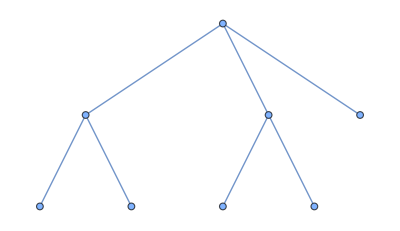
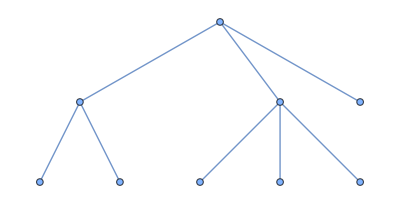
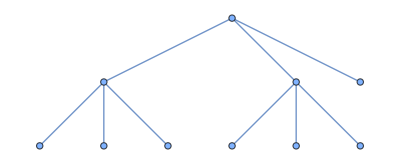

```mathematica
addVertices[graphlist_]:=Module[{graphs},graphs=ParallelMap[Function[g,Flatten[Table[With[{v=VertexList[g][[i]]},If[VertexDegree[g,v]==1,{Graph[Join[EdgeList[g],{v<->(VertexCount[g]+1),v<->(VertexCount[g]+2)}]],Graph[Join[EdgeList[g],{v<->(VertexCount[g]+1),v<->(VertexCount[g]+2),v<->(VertexCount[g]+3)}]]},Nothing]],{i,VertexCount[g]}]]],graphlist];
DeleteDuplicatesBy[Flatten[graphs],CanonicalGraph]]
(* Defining the foundational graphs without any internal lines/propagators, i.e. a cubic vertex and a quartic vertex *)
prop[0]={Graph[{UndirectedEdge[2, 1], UndirectedEdge[3, 1], UndirectedEdge[4, 1]}],Graph[{UndirectedEdge[2, 1], UndirectedEdge[3, 1], UndirectedEdge[4, 1],UndirectedEdge[5, 1]}]};

(* Nesting process to generate graphs by repeatedly appling addVertices function, where the initial graph is prop[0] *)
NumberofPropagators=3; (* determines how many times addVertices will be applied; change this number accordingly *)
props=Flatten[NestList[addVertices,prop[0],NumberofPropagators]]
```

These are all possible tree-level graphs with up to three internal lines. The code is fast enough to go to much higher number of propagators. In any case, one just needs to run it once up to some NumberofPropagators >> 1 and save it in a file for future use.

In the next step, we use FeynArts (https://feynarts.de/) to thread fermion lines through these graphs, so we have to specify the number of external fermions and bosons. We will use four fermions and two scalars as an example.
First we load FeynArts, make sure the FeynArts model file “FeynArtsToyModel.mod” is in the notebook directory. It specifies that fermions F and scalars S can only have vertices of the form FFS, SSS, SSSS.
Make sure to cite FeynArts/FeynCalc (https://feyncalc.github.io/) appropriately when using this code for research.

```mathematica
(* To install FeynCalc/FeynArts in Mathematica, execute the following commands: *)
Import["https://raw.githubusercontent.com/FeynCalc/feyncalc/master/install.m"]; 
InstallFeynCalc[]
```

```mathematica
(* Run this to load FeynArts *)
description="Topology, tree level"; 
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;
Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"FeynArts"}; 
Get["FeynCalc`"];
$FAVerbose=0;
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

SetDelayed::wrsym: Symbol Discard is Protected.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

First define incoming particles and put in the list, F[1] and S[1] represents fermion and scalar. Our convention is to always list scalars first.

```mathematica
ListofincomingParticles={S[1],S[1],F[1],F[1],F[1],F[1]};
NumberofExternalParticles=Length[ListofincomingParticles];
```

Then we pick all graphs in “props” that have six external particles and store them in “topology”:

```mathematica
NumberOfExternalParticles[graph_]:=Count[VertexDegree[graph],1]
topology=Select[props,NumberOfExternalParticles[#]==NumberofExternalParticles&]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Now we convert these diagrams to FeynArts’ notation:

```mathematica
treeX=topL[top[1]/@ParallelTable[ Module[{OE,outerEdges,IncomX,remainingEdges,InterX,list,listX},
OE=Select[EdgeList[topology[[i]]],VertexDegree[topology[[i]],First[#]]==1||VertexDegree[topology[[i]],Last[#]]==1&] (* selecting the outer incoming particles *) ;
outerEdges=Map[Sort[#,Greater]&,OE/.a_<->b_/;Count[OE[[All,1]],a]>1:>b<->a] (* reordering the the list OE such that it is ascending order; required by FeynArts *);
IncomX= outerEdges/.a_<->b_ -> Propagator[Incoming][Vertex[1][a],Vertex[3][b+4]] (* Making the incoming particles like FeynArts file *);
remainingEdges=Complement[EdgeList[topology[[i]]],OE] (* This is to identify the propagator *);
InterX=remainingEdges/.a_<->b_ -> Propagator[Internal][Vertex[3][a+4],Vertex[3][b+4]] (* Making the incoming particles like FeynArts file *);
list=Join[IncomX,InterX]
]
,{i,1,Length[topology]}]/.top[n_][list_List]:>Topology[n][Sequence@@list]]/.topL[list_]:>TopologyList[Sequence@@list];
```

Now we thread the external particles through these diagrams in all ways allowed by the FFS, SSS, SSSS vertices:

```mathematica
(* need to do permutation of incoming particles to get all the topologies, such that scalars are properly placed with all the permutations *)
IncomingParticles=Permutations[ListofincomingParticles] ;
(* Defining the FeynArts code to insert incoming particles, 
IncomingParticles[[i]]->{} simily means all the particles are going to a single vertex
Model->"FeynArtsToyModel" imports the model file that has 3 point and 4 point vertices FFS,SSS,SSSS*)
diagsTreeX=ParallelTable[InsertFields[treeX,IncomingParticles[[i]]->{},InsertionLevel->{Classes},Model->"FeynArtsToyModel"],
{i,1,Length[IncomingParticles]}] (* Here FeynArts assigns the topology with the model file "Toymodel" *);
```

Next, we generate a list of graphs (Feynman diagrams) by taking data from diagsTreeX. 
We also sort particle names so that scalars come before fermions, but beyond that the particle ordering is arbitrary. 
Internal lines are colored red; fermion lines are solid and boson lines are dashed.

```mathematica
listXX = Flatten[
Table[
Module[{diagram,diagramX},
diagramX=diagsTreeX[[l,i]][[1]]/.Table[diagsTreeX[[l,i]][[2]][[1,1]][[k]],{k,Length[diagsTreeX[[l,i]][[2]][[1,1]]]}];
  diagram=SortBy[diagramX,If[MemberQ[#,S[1]],0,1]&];(* This is to make the output for incomping particles such that scalars are always before fermions; not really necessary but relevant for UV completion code *);
(* A graph is constructed using Graph[..] where the vertices and edges are determined by the "diagram" defined above, 
EdgeStyle defines the style depending on type of particle interaction 
EdgeColors categorizes the edges into different color codes based on particles *)
{Graph[Table[ToString[diagram[[j]][[1]]]<->ToString[diagram[[j]][[2]]],{j,Length[diagram]}],EdgeStyle->Table[ToString[diagram[[j]][[1]]]<->ToString[diagram[[j]][[2]]]->Which[ToString[diagram[[j]][[3]]]=="F[1]",Black,ToString[diagram[[j]][[3]]]=="S[1]",{Black,Dashed},ToString[diagram[[j]][[3]]]=="F",Red,ToString[diagram[[j]][[3]]]=="S",{Red,Dashed}],{j,Length[diagram]}],
EdgeLabels->Table[ToString[diagram[[j]][[1]]]<->ToString[diagram[[j]][[2]]]-> Placed[Text[ToString[j],Background->White],{Left,"Middle"}],{j,Length[diagram]}]],"EdgeColors"->Table[Which[ToString[diagram[[j]][[3]]]=="F[1]",1,ToString[diagram[[j]][[3]]]=="S[1]",2,ToString[diagram[[j]][[3]]]=="F",3,ToString[diagram[[j]][[3]]]=="S",4],{j,Length[diagram]}]}
]
,{l,1,Length[diagsTreeX]},{i,1,Length[diagsTreeX[[l]]]}],1];
Print["Number of topologies:  ",Length[listXX]];
```

Number of topologies:  31

The output contains topologically equivalent diagrams, so we load and use IGraphM (https://github.com/szhorvat/IGraphM) to eliminate them.
Make sure to cite IGraphM appropriately when using this code for research.

```mathematica
(* To install IGraphM: *)
Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]
```

```mathematica
Get["IGraphM`"];
```

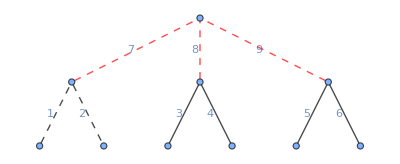
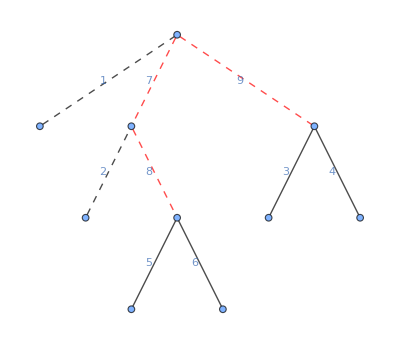
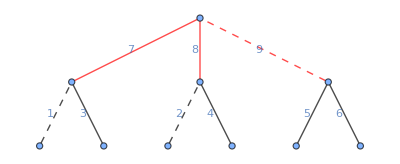
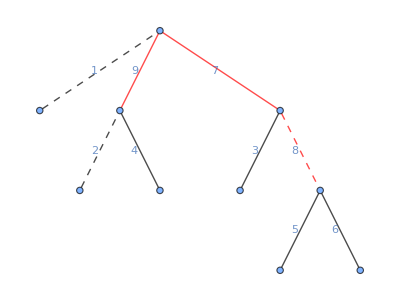
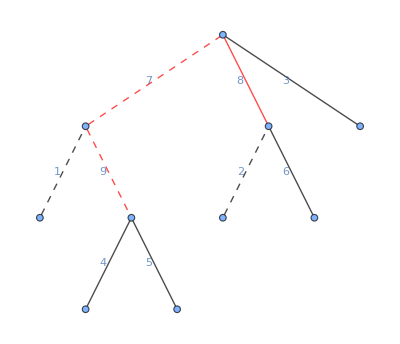
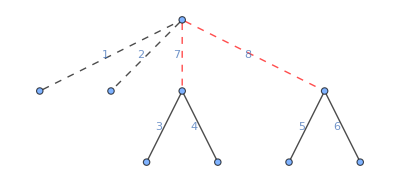
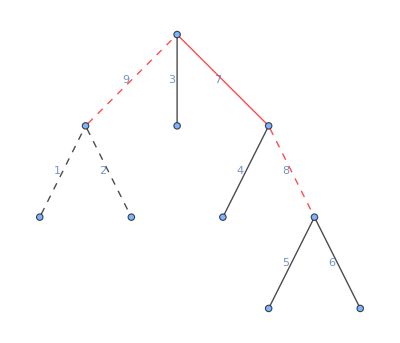
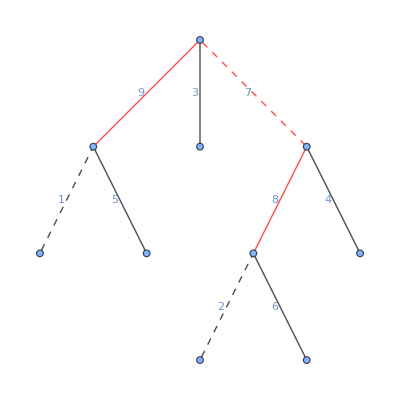
(-Graphics- | EdgeColors→{2,2,1,1,1,1,4,4,4}
-Graphics- | EdgeColors→{2,2,1,1,1,1,4,4,4}
-Graphics- | EdgeColors→{2,2,1,1,1,1,3,3,4}
-Graphics- | EdgeColors→{2,2,1,1,1,1,3,4,3}
-Graphics- | EdgeColors→{2,2,1,1,1,1,4,3,4}
-Graphics- | EdgeColors→{2,2,1,1,1,1,4,4}
-Graphics- | EdgeColors→{2,2,1,1,1,1,3,4,4}
-Graphics- | EdgeColors→{2,2,1,1,1,1,4,3,3})

Number of Irreducible topology:  8

```mathematica
irred=DeleteDuplicates[listXX,IGVF2IsomorphicQ[#1,#2]&]
Print["Number of Irreducible topology:  ",Length[irred]];
```

Et voila, all topologically inequivalent tree-level Feynman diagrams with two external bosons and four external fermions.

## Particle numbering

For our UV completion code, it is useful to extract some information from each diagram and store it together with the graph. For one, we collect whether particle 1, 2, 3, etc are external scalars (S), external fermions (F), internal new bosons (NB), or internal new fermions (NF). Second, we collect which particles meet at each vertex. For example, for  we collect the vertex structure {{1, 2, 5}, {3, 4, 5}} that tells us that particles 1,2, and 5 meet at one vertex, and 3, 4 and 5 meet at another. Any particle number that only occurs once in this list is an external particle, every particle number that occurs twice is an internal particle.

```mathematica
(* This code processes a list of irreducible diagrams ("irred"), reindexes the edges and classifies particles in each diagram *)
Flist=ParallelTable[
irreddiagram=irred[[s]];
vertices={};
For[n=1,n<=Length[VertexList[irreddiagram[[1]]]],n++,
(*Checking whether the vertex represents an interaction with more than two particles. If this is true, it processes that vertex. *)
If[ToExpression[VertexList[irreddiagram[[1]]]][[n,0,1]]>2,
vertex={};
For[m=1,m<=Length[EdgeList[irreddiagram[[1]]]],m++,
If[EdgeList[irreddiagram[[1]]][[m]][[1]]==VertexList[irreddiagram[[1]]][[n]]||EdgeList[irreddiagram[[1]]][[m]][[2]]==VertexList[irreddiagram[[1]]][[n]],
AppendTo[vertex,EdgeList[irreddiagram[[1]]][[m]]];
]
];
If[Length[vertex]>0,AppendTo[vertices,vertex]]
]
];
(* classify the particles and sort the vertices by their second to last element *)
Vertx=vertices/.Table[EdgeList[irreddiagram[[1]]][[k]]->k,{k,1,Length[EdgeList[irreddiagram[[1]]]]}];
{irreddiagram[[1]],irreddiagram[[2,2]]/.{1->"F",2->"S",3->"NF",4->"NB"},Sort/@SortBy[Vertx,#[[-2]]&]},
{s,1,Length[irred]}]
```

(-Graphics- | {S,S,F,F,F,F,NB,NB,NB} | (1 | 2 | 7
3 | 4 | 8
5 | 6 | 9
7 | 8 | 9)
-Graphics- | {S,S,F,F,F,F,NB,NB,NB} | (3 | 4 | 9
5 | 6 | 8
1 | 7 | 9
2 | 7 | 8)
-Graphics- | {S,S,F,F,F,F,NF,NF,NB} | (1 | 3 | 7
2 | 4 | 8
5 | 6 | 9
7 | 8 | 9)
-Graphics- | {S,S,F,F,F,F,NF,NB,NF} | (2 | 4 | 9
5 | 6 | 8
1 | 7 | 9
3 | 7 | 8)
-Graphics- | {S,S,F,F,F,F,NB,NF,NB} | (4 | 5 | 9
2 | 6 | 8
1 | 7 | 9
3 | 7 | 8)
-Graphics- | {S,S,F,F,F,F,NB,NB} | {{3,4,7},{5,6,8},{1,2,7,8}}
-Graphics- | {S,S,F,F,F,F,NF,NB,NB} | (1 | 2 | 9
5 | 6 | 8
3 | 7 | 9
4 | 7 | 8)
-Graphics- | {S,S,F,F,F,F,NB,NF,NF} | (1 | 5 | 9
2 | 6 | 8
3 | 7 | 9
4 | 7 | 8))

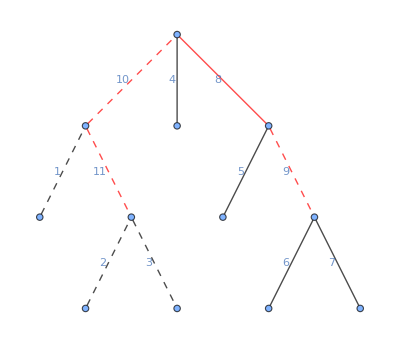
For our UV completion code, it is convenient to ensure the following particle numbering: 
label the incoming particles and propagators such that each n-particle vertex {A[1],A[2],...,A[n]} contains n-1 known fields A[1],...,A[n-1], so either external fields or internal fields that have already appeared at a previous vertex. 
This allows us to systematically go through the list of vertices and only have at most one unknown (internal) particle A[n].
In some cases, this numbering comes out automatically, but this is not always the case. Take for example this four-fermion three-scalar diagram
{-Graphics-,{"S","S","S","F","F","F","F","NF","NB","NB","NB"},{{2,3,11},{6,7,9},{4,8,10},{5,8,9},{1,10,11}}}
Our UV completion code would start with the first vertex and multiply particles 2 and 3 together to get the quantum numbers of particle 11. So far, so good. The second vertex gives us the quantum numbers of particle 9, also fine. But the third vertex {4,8,10} contains only one known particle (4) and two unknowns (8 & 10). In order to allow our code to sequentially go through the vertex list without this happening, we will swap particle numbers until our desired ordering is achieved. 

The following code swaps particle numbers in a graph, in the {S,S,..., F,F,.. NB,..NF} list, and in the vertex list {{A,B,C},{..},{...}}. Notice that our labeling/sorting is not unique.

```mathematica
label[i_]:=Placed[Text[ToString[i],Background->White],{Left,"Middle"}]
(*code that swaps particles x and y in diagram, spin list, and vertex list:*)
swap[list_,x_,x_]:={list[[1]],list[[2]],SortBy[SortBy[#,Abs]&/@list[[3]],N@*Last]}
swap[list_,x_,y_]:={IGEdgeMap[Replace[{label[x]->label[y],label[y]->label[x]}],EdgeLabels,list[[1]]],Permute[list[[2]],Cycles[{{x,y}}]],SortBy[SortBy[#,Abs]&/@(list[[3]]/.(x->temp)/.(y->x)/.(temp->y)),N@*Last]}
SortDiagram[list_]:=Module[{templist=swap[list,1,1](*make sure input has properly sorted vertex list*),NumberOfExternal,NumberOfInternal,mismatch,swap1,swap2,goal,NumberOfSwaps=0},
NumberOfInternal=Count[list[[2]],"NB"]+Count[list[[2]],"NF"];
NumberOfExternal=Count[list[[2]],"S"]+Count[list[[2]],"F"];
(*Sort everything so that list[[3]][[All,3]] looks like {8,9,10,11,...,20,21,22,22}, so the goal is to reach this list:*);
goal=Join[Range[NumberOfExternal+1,NumberOfExternal+NumberOfInternal],{NumberOfExternal+NumberOfInternal}];
(*mismatch is how far away we are from the goal, i.e. which internal particles are not in place*);
mismatch=Join[Fold[DeleteCases[##,1,1]&,Last[#]&/@templist[[3]],goal],Fold[DeleteCases[##,1,1]&,goal,Last[#]&/@templist[[3]]]];
While[Length[mismatch]!=0,
(*of all the mismatched particles, pick two at random to switch around and then repeat. Random so that we never end up in a loop where we switch the same two particles around without changing anything.*)
{swap1,swap2}=RandomSample[mismatch,2];
templist=swap[templist,swap1,swap2];
mismatch=Join[Fold[DeleteCases[##,1,1]&,Last[#]&/@templist[[3]],goal],Fold[DeleteCases[##,1,1]&,goal,Last[#]&/@templist[[3]]]];
NumberOfSwaps++;
(*If I ever need more than a 100 swaps something is wrong, so this breaks the infinity loop:*);
If[NumberOfSwaps>=100,Print["Can't sort this!"];Abort[];]
];
templist
]
```

And now we apply it to our previously generated list “Flist”:

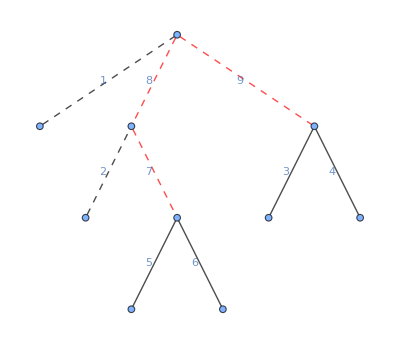
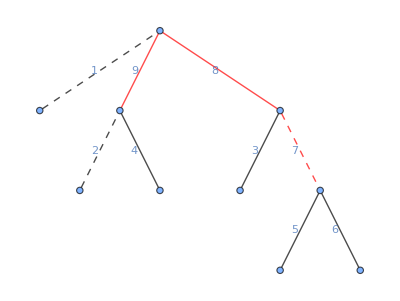
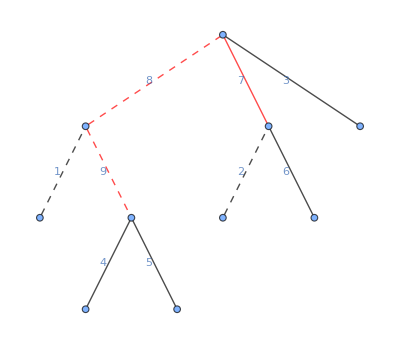
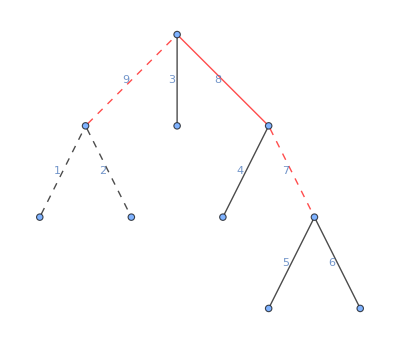
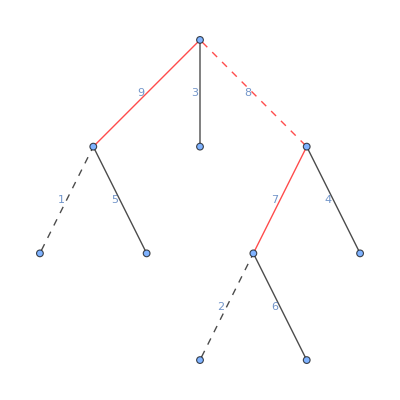
(-Graphics- | {S,S,F,F,F,F,NB,NB,NB} | (1 | 2 | 7
3 | 4 | 8
5 | 6 | 9
7 | 8 | 9)
-Graphics- | {S,S,F,F,F,F,NB,NB,NB} | (5 | 6 | 7
2 | 7 | 8
1 | 8 | 9
3 | 4 | 9)
-Graphics- | {S,S,F,F,F,F,NF,NF,NB} | (1 | 3 | 7
2 | 4 | 8
5 | 6 | 9
7 | 8 | 9)
-Graphics- | {S,S,F,F,F,F,NB,NF,NF} | (5 | 6 | 7
3 | 7 | 8
1 | 8 | 9
2 | 4 | 9)
-Graphics- | {S,S,F,F,F,F,NF,NB,NB} | (2 | 6 | 7
3 | 7 | 8
1 | 8 | 9
4 | 5 | 9)
-Graphics- | {S,S,F,F,F,F,NB,NB} | {{3,4,7},{5,6,8},{1,2,7,8}}
-Graphics- | {S,S,F,F,F,F,NB,NF,NB} | (5 | 6 | 7
4 | 7 | 8
1 | 2 | 9
3 | 8 | 9)
-Graphics- | {S,S,F,F,F,F,NF,NB,NF} | (2 | 6 | 7
4 | 7 | 8
1 | 5 | 9
3 | 8 | 9))

```mathematica
Fulllistoftopologies=ParallelTable[SortDiagram[Flist[[i]]],{i,Length[Flist]}]
```

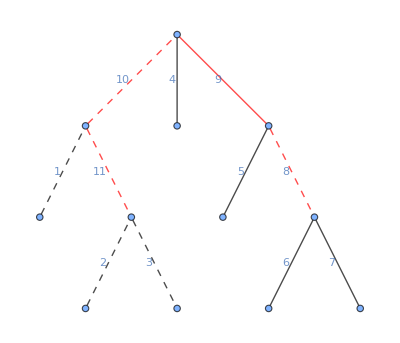
These are the properly ordered topologically irreducible diagrams we employ in our UV completion code. Notice, in particular, that the four-fermion three-scalar diagram from before indeed comes out properly ordered now after doing the swapping:
{-Graphics-,{"S","S","S","F","F","F","F","NB","NF","NB","NB"},{{6,7,8},{5,8,9},{4,9,10},{1,10,11},{2,3,11}}}

“Fulllistoftopologies” can now be exported and used for any operator involving the same number of external bosons and fermions. We provide such exported topology files for most cases of interest in addition to this notebook, but others can easily be generated as shown here.

## Side note: full topology from graph

The topology entries such as
{-Graphics-,{"S","S","S","F","F","F","F","NB","NF","NB","NB"},{{6,7,8},{5,8,9},{4,9,10},{1,10,11},{2,3,11}}}
provide redundant information for the sake of making the UV-completion code faster. The entries {“S”, “S”, “S”, “F”, “F”, “F”, “F”, “NB”, “NF”, “NB”, “NB”} and {{6, 7, 8}, {5, 8, 9}, {4, 9, 10}, {1, 10, 11}, {2, 3, 11}} can be constructed from the graph alone, here is a code that does exactly that:

```mathematica
(*Takes a graph, e.g. the first entry of a UVCompletion[..] output, and converts it into the full topology: {graph, {"S",..,"F",..,"NF",..,"NB",..},{vertices}}.*)
ConvertGraphToTopology[g_Graph]:=Module[{edges,labels,styles,classifyEdge,vertexAdjacency,vertexStructure},(*Extract edge labels*)labels=Association@Cases[PropertyValue[g,EdgeLabels],Rule[UndirectedEdge[a_,b_],Placed[Text[label_,___],___]]:>(UndirectedEdge[a,b]->ToExpression[label]),{1}];
(*Extract edge styles*)
styles=Association@Cases[PropertyValue[g,EdgeStyle],Rule[e_UndirectedEdge,s_]:>(e->Flatten[{s}]),{1}];
(*Function to classify edges*)classifyEdge[e_]:=Module[{s=Lookup[styles,e,{}]},Which[MemberQ[s,GrayLevel[0]]&&!MemberQ[s,Dashing[{Small,Small}]],"F",MemberQ[s,GrayLevel[0]]&&MemberQ[s,Dashing[{Small,Small}]],"S",MemberQ[s,RGBColor[1,0,0]]&&!MemberQ[s,Dashing[{Small,Small}]],"NF",MemberQ[s,RGBColor[1,0,0]]&&MemberQ[s,Dashing[{Small,Small}]],"NB",True,"Unknown"]];
(*Extract and sort edges by label*)
edges=SortBy[Keys[labels],labels];
(*Build vertex adjacency structure correctly*)vertexAdjacency=GroupBy[Flatten[Keys[labels]/. UndirectedEdge[a_,b_]:>{a->labels[UndirectedEdge[a,b]],b->labels[UndirectedEdge[a,b]]}],First->Last,Union];
(*Extract only unique sorted lists of edge labels where vertices share multiple edges*)vertexStructure=SortBy[Select[Values[vertexAdjacency],Length[#]>1&],Last];
(*Return full structure*){g,Table[classifyEdge[e],{e,edges}],vertexStructure}
];
```

For example,

```mathematica
ConvertGraphToTopology[-Graphics-]//StandardForm
```

{-Graphics-,{S,S,S,F,F,F,F,NB,NF,NB,NB},{{6,7,8},{5,8,9},{4,9,10},{1,10,11},{2,3,11}}}

generates the standard topology file that includes {“S”, “S”, “S”, “F”, “F”, “F”, “F”, “NB”, “NF”, “NB”, “NB”} and {{6, 7, 8}, {5, 8, 9}, {4, 9, 10}, {1, 10, 11}, {2, 3, 11}}. 
The reverse is true as well: the graph can be constructed from the information in {“S”, “S”, “S”, “F”, “F”, “F”, “F”, “NB”, “NF”, “NB”, “NB”} and {{6, 7, 8}, {5, 8, 9}, {4, 9, 10}, {1, 10, 11}, {2, 3, 11}}, which makes for a more compact topology definition that is also not reliant on Mathematica. We provide topologies in that format in “topology text files”, which also define the topology names, e.g. dim7-4F-1S.dat contains
T[7][1]	{“S”, “F”, “F”, “F”, “F”, “NB”, “NB”}	{{2, 3, 6}, {1, 6, 7}, {4, 5, 7}}
T[7][2]	{“S”, “F”, “F”, “F”, “F”, “NF”, “NB”}	{{1, 3, 6}, {2, 6, 7}, {4, 5, 7}}
which defines the name T[operator mass dimension d][topology] and the topology structure.

## Side note: directed graphs and momentum flow

The third entry in our topology files, e.g.  {{6, 7, 8}, {5, 8, 9}, {4, 9, 10}, {1, 10, 11}, {2, 3, 11}}, defines the charge or momentum flow through our diagram. We treat all external particles as incoming, and internal particles flow from the first vertex they appear in to the second. So in this example, the internal particle 8 goes from the vertex {6, 7, 8} to {5, 8, 9}, i.e. it is outgoing at the first vertex and incoming at the second. We can show this explicitly in the graph using arrows or directed edges. 

The code below provides the function MomentumGraph, which takes a graph like  as input and returns a graph with proper momentum arrows that match the rule {{6, 7, 8}, {5, 8, 9}, {4, 9, 10}, {1, 10, 11}, {2, 3, 11}}:

```mathematica
(*Takes a graph,e.g.the first entry of a UVCompletion[..] output,and converts it into the full topology:{graph,{"S",..,"F",..,"NF",..,"NB",..},{vertices}}.*)ConvertGraphToTopology[g_Graph]:=Module[{edges,labels,styles,classifyEdge,vertexAdjacency,vertexStructure},(*Extract edge labels*)labels=Association@Cases[PropertyValue[g,EdgeLabels],Rule[UndirectedEdge[a_,b_],Placed[Text[label_,___],___]]:>(UndirectedEdge[a,b]->ToExpression[label]),{1}];
(*Extract edge styles*)styles=Association@Cases[PropertyValue[g,EdgeStyle],Rule[e_UndirectedEdge,s_]:>(e->Flatten[{s}]),{1}];
(*Function to classify edges*)classifyEdge[e_]:=Module[{s=Lookup[styles,e,{}]},Which[MemberQ[s,GrayLevel[0]]&&!MemberQ[s,Dashing[{Small,Small}]],"F",MemberQ[s,GrayLevel[0]]&&MemberQ[s,Dashing[{Small,Small}]],"S",MemberQ[s,RGBColor[1,0,0]]&&!MemberQ[s,Dashing[{Small,Small}]],"NF",MemberQ[s,RGBColor[1,0,0]]&&MemberQ[s,Dashing[{Small,Small}]],"NB",True,"Unknown"]];
(*Extract and sort edges by label*)edges=SortBy[Keys[labels],labels];
(*Build vertex adjacency structure correctly*)vertexAdjacency=GroupBy[Flatten[Keys[labels]/. UndirectedEdge[a_,b_]:>{a->labels[UndirectedEdge[a,b]],b->labels[UndirectedEdge[a,b]]}],First->Last,Union];
(*Extract only unique sorted lists of edge labels where vertices share multiple edges*)vertexStructure=SortBy[Select[Values[vertexAdjacency],Length[#]>1&],Last];
(*Return full structure*){g,Table[classifyEdge[e],{e,edges}],vertexStructure}]

MakeDirectedGraph[g_Graph] :=Graph[DirectedEdge@@@EdgeList[g],{EdgeLabels->(EdgeLabels/. Options[g,EdgeLabels])/. Rule[UndirectedEdge[a_,b_],val_]:>Rule[DirectedEdge[a,b],val],EdgeStyle->(EdgeStyle/. Options[g,EdgeStyle])/. Rule[UndirectedEdge[a_,b_],val_]:>Rule[DirectedEdge[a,b],val]}]



FlipEdgeByLabel[g_Graph,labelText_]:=Module[{edges,labelsRaw,stylesRaw,labelsList,stylesList,targetPairs,keys,revKeys,mapping,newEdges,newLabels,newStyles,otherOpts,extractText,canon},(*helper:extract visible text from label objects*)extractText[Placed[Style[Text[x_,___],___],___]]:=x;
extractText[Placed[Text[x_,___],___]]:=x;
extractText[Text[x_,___]]:=x;
extractText[x_]:=x;
(*canonicalize label for matching (so 5 and "5" compare equal)*)canon[x_]:=If[StringQ[x],x,ToString[x,InputForm]];
(*1) get edge list and existing label/style rules (safe defaults)*)edges=EdgeList[g];
labelsRaw=EdgeLabels/. Options[g]/. EdgeLabels->{};
stylesRaw=EdgeStyle/. Options[g]/. EdgeStyle->{};
(*ensure we have lists of rules (not Associations)*)labelsList=If[MatchQ[labelsRaw,_Rule|_RuleDelayed],{labelsRaw},labelsRaw];
stylesList=If[MatchQ[stylesRaw,_Rule|_RuleDelayed],{stylesRaw},stylesRaw];
(*3) find label rule(s) whose visible text matches (robust to 5 vs "5")*)targetPairs=Select[labelsList,canon[extractText[#[[2]]]]===canon[labelText]&];
(*nothing found->return original graph unchanged*)If[targetPairs==={},Return[g]];
(*4) build mapping oldEdge->reversedEdge (handle Directed/Undirected)*)keys=targetPairs[[All,1]];
revKeys=keys/. {DirectedEdge[a_,b_]:>DirectedEdge[b,a],UndirectedEdge[a_,b_]:>UndirectedEdge[b,a]};
mapping=Thread[keys->revKeys];
(*5) apply mapping to edges and rule keys using Replace (/.),not ReplacePart*)newEdges=Replace[edges,mapping,{1}];
newLabels=labelsList/. mapping;
newStyles=stylesList/. mapping;
(*6) preserve other options and rebuild graph*)otherOpts=DeleteCases[Options[g],(EdgeLabels->_)|(EdgeStyle->_)];
Graph[newEdges,Sequence@@otherOpts,EdgeLabels->newLabels,EdgeStyle->newStyles]]



FixEdgeDirections[g0_Graph,clusters_List]:=Module[{newg=g0,extractText,canon,verts,labelsRaw,labels,vertexLabelSets,uniqueLabels,posIndices,i,j,clLeftCanon,clRightCanon,vFrom,vTo,edgeRule,srcdst,flipped={},lab,ReturnFlipped=False,labelsFromGraph,clCanon,vHub},(*---helpers---*)extractText[Placed[Text[x_,___],___]]:=x;
extractText[Text[x_,___]]:=x;
extractText[x_]:=x;
(*canonicalize so 7 and "7" compare equal*)canon[x_]:=If[StringQ[x],x,ToString[x]];
(*build a fresh labels map from the current graph*)labelsFromGraph[gg_]:=Module[{lr=EdgeLabels/. Options[gg]/. EdgeLabels->{}},lr/. (Rule|RuleDelayed)[UndirectedEdge[a_,b_],v_]:>Rule[DirectedEdge[a,b],v]];
(*---prepare vertex incident-label sets (order-independent,canonicalized)---*)labels=labelsFromGraph[newg];
verts=VertexList[newg];
vertexLabelSets=AssociationThread[verts,Table[Sort[DeleteDuplicates[canon/@(extractText/@Cases[Normal[labels],Rule[DirectedEdge[a_,b_],val_]/;(a===v||b===v):>val])]],{v,verts}]];
(*unique labels appearing somewhere in clusters*)uniqueLabels=DeleteDuplicates[Flatten[clusters]];
(*iterate over each label occurring in clusters*)Do[lab=uniqueLabels[[k]];
posIndices=Flatten[Table[If[MemberQ[clusters[[t]],lab],t,Nothing],{t,Length[clusters]}]];
If[Length[posIndices]<1,Continue[]];
labels=labelsFromGraph[newg];
edgeRule=FirstCase[Normal[labels],Rule[e_,val_]/;canon[extractText[val]]===canon[lab]:>e,Missing["NoSuchLabel"]];
If[edgeRule===Missing["NoSuchLabel"],Continue[]];
srcdst=List@@edgeRule;
If[Length[posIndices]===1,(*Leaf/external:always point toward the hub*)clCanon=Sort[canon/@clusters[[posIndices[[1]]]]];
vHub=FirstCase[Keys[vertexLabelSets],v_/;vertexLabelSets[v]===clCanon:>v,Missing["NoHub"]];
If[vHub===Missing["NoHub"],Continue[]];
If[srcdst[[2]]=!=vHub,newg=FlipEdgeByLabel[newg,lab];AppendTo[flipped,lab]],(*Internal:point from earlier cluster hub to later cluster hub*)i=Min[posIndices];j=Max[posIndices];
clLeftCanon=Sort[canon/@clusters[[i]]];
clRightCanon=Sort[canon/@clusters[[j]]];
vFrom=FirstCase[Keys[vertexLabelSets],v_/;vertexLabelSets[v]===clLeftCanon:>v,Missing["NoHub"]];
vTo=FirstCase[Keys[vertexLabelSets],v_/;vertexLabelSets[v]===clRightCanon:>v,Missing["NoHub"]];
If[vFrom===Missing["NoHub"]||vTo===Missing["NoHub"],Continue[]];
If[srcdst[[1]]=!=vFrom,newg=FlipEdgeByLabel[newg,lab];AppendTo[flipped,lab]]],{k,Length[uniqueLabels]}];
If[ReturnFlipped,{newg,flipped},newg]]

(*Final function, takes one of our normal graphs and returns a graph with correct momentum arrows:*)
MomentumGraph[g_Graph]:=FixEdgeDirections[MakeDirectedGraph[g],ConvertGraphToTopology[g][[3]]]
```

Try this out on some topology; momentum flows from top to bottom according to arrows:

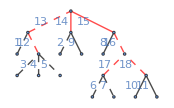
```mathematica
examplegraph=-Graphics-;
ConvertGraphToTopology[examplegraph]
MomentumGraph[examplegraph]
```

{-Graphics-,{S,S,S,S,S,S,S,F,F,F,F,NB,NB,NF,NF,NB,NB,NB},{{3,4,5,12},{1,12,13},{2,9,14},{13,14,15},{8,15,16},{6,7,17},{10,11,18},{16,17,18}}}